```mathematica
S[t_]= Round[t/4-0.5];(*Step Function*)
```

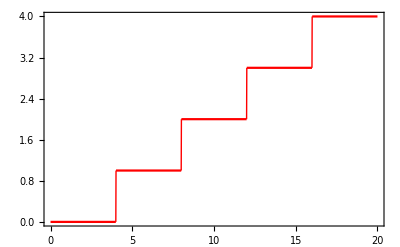

```mathematica
p1=Plot[S[t],{t,0,20},ExclusionsStyle->{{Thick,Red}},PlotStyle->Red,FrameTicks->{None,None,None,All},ImagePadding->{{50,50},{20,2}},Frame->{False,False,False,True}]
```

```mathematica
sys1:= D[X[t],t]==  S[t]- X[t](*pdes *)
sys2 := D[R[t],t]== 2* S[t] -2* X[t] *R[t]
```

```mathematica
r=NDSolve[{sys1,sys2,X[0]==0,R[0]==1 },{R},{t,0,20}];(*solutions of pdes*)
x=NDSolve[{sys1,sys2,X[0]==0,R[0]==1 },{X},{t,0,20}];
```

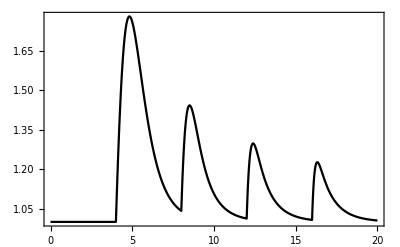
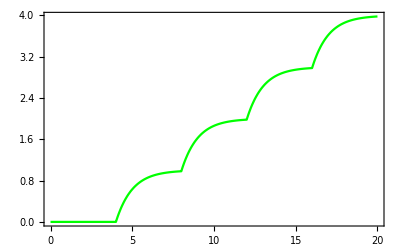
-Graphics--Graphics--Graphics-

```mathematica
p2=Plot[Evaluate[R[t]/.r],{t,0,20},PlotRange->All,Frame->True,ImagePadding->{{50,50},{20,2}},PlotStyle->Black];
p3=Plot[Evaluate[X[t]/.x],{t,0,20},ExclusionsStyle->{Thick},PlotStyle->Green,Ticks->{{},{0,1,2,3,4,5}},ImagePadding->{{50,50},{20,2}},FrameTicks->{None,None,None,All},Frame->{False,False,False,True}];
Overlay[{p1,p2,p3}]
```

```mathematica
p1=Plot[{2S/.S->1,2S/. S->2,2S/.S->3},{x,0,2},Frame->True,PlotRange->{{0,2},{0,8}},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Green,Dashed}}];(*positive part*)
```

```mathematica
p2=Plot[{2 X R[t]/.X->1,2 X R[t]/. X->2,2 X R[t]/.X->3},{R[t],0,2},Frame->True,PlotRange->{{0,2},{0,8}},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}}];(*negative part*)
```

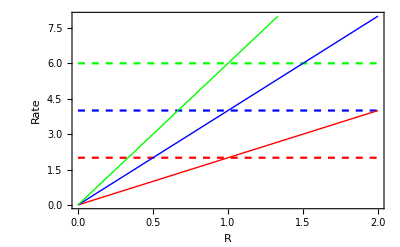

```mathematica
Show[{p1,p2},FrameLabel->{"R","Rate"}]
```

```mathematica
Show[%24,PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```